# Lattice Calculations

## Constants

```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .529177*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;

el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
kK=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;

λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 282*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency clock trans ??? *)
```

## Axial Beam Parameters

```mathematica
f=3cm; (* Final lens f*)
λ813 = 813nm;
θ=20 Degree;(* 2θ max angular sep. of beams *)
d =Tan[θ]f;(* Separation of spots = 2d*)
k=2Pi/λ813;
Pbeam=.75; (*power/beam in watts*)

wx0 = 75 μm;(* Desired beam waists at lattice*)
wy0 = wx0*(Sin[θ]);
```

## Axial optics calcs

```mathematica
{wx, wy}=f λ813/(Pi {wx0,wy0})//N (* Waists into 3cm lens *)
```

{0.000103514,0.000302656}

```mathematica
l=95 cm;
wf = 5.5 μm/2; (* MFR of Oz fiber*)
fcoll = wy*wf*Pi/λ813 (*f of collimating lens*)
NA = λ813/(Pi wf)(* NA of Oz fiber *)
```

0.00321618

0.094104

Cylindrical final lens:

```mathematica
25cm*λ813/(Pi wx0)//N
3cm*λ813/(Pi wy0)//N
```

0.00086262

0.000302656

Cylindrical lenses with shared focal plane

```mathematica
Pi wx0 wy/λ813//N
```

0.0877141

### Single beam case

```mathematica
Ulattice = (α Pbeam)/(ϵ0 c π wx0*wy0) ;(*Note factor of 4 difference from retroed lattice*)
TrapDepthuK = 10^6 Ulattice/kB
```

15.7507

```mathematica
ftrap = 1/(π wy0)√(Ulattice/m)
ωtrap = 2π ftrap;
```

481.407

```mathematica
x0=Sqrt[ℏ/(m ωtrap)]
T0=30μK;
u0=Sqrt[(kB T0)/(m ωtrap^2)]
```

4.91335×10^-7

0.0000177008

```mathematica
u0/λp
```

0.0000177008/λp

### Tight lattice case

```mathematica
Ulattice = (4 α Pbeam)/(ϵ0 c π wx0*wy0) ;
TrapDepthuK = 10^6 Ulattice/kB
TrapDepthHz = 1/(2π)Ulattice/ℏ;
λp = λ813/(2Sin[θ]);
ftrap = 1/λp √((2*Ulattice)/m)
ωtrap = 2π ftrap;
kl = (2Pi)/(2 λp);
Er = (ℏ kl)^2/(2m);
Ulattice/Er
```

63.0027

92323.4

3231.93

### Loose lattice case

```mathematica
d =1mm;
θloose=ArcTan[d/f];
Ulattice = (4 α Pbeam)/(ϵ0 c π wx0*wy0) ;
TrapDepthuK = 10^6 Ulattice/kB;
TrapDepthHz = 1/(2π)Ulattice/ℏ;
λp = λ813/(2Sin[θloose]);
ftrap = 1/λp √((2*Ulattice)/m)
ωtrap = 2π ftrap;
kl = (2Pi)/(2 λp);
Er = (ℏ kl)^2/(2m);
Ulattice/Er
```

8992.85

340635.

```mathematica
J = 4/(√π)Er(Ulattice/Er)^(3/4)Exp[-2 √(Ulattice/Er)];
Jhz = J/(2π ℏ)
```

1.3976611392831×10^-502

```mathematica
x0=Sqrt[ℏ/(m ωtrap)]
T0=30μK;
u0=Sqrt[(kB T0)/(m ωtrap^2)]
```

1.1368×10^-7

9.47565×10^-7

```mathematica
λp/wy0//N
```

0.475675

## Tunneling

Deep lattice case, entirely suppressed:

```mathematica
J = 4/(√π)Er(Ulattice/Er)^(3/4)Exp[-2 √(Ulattice/Er)];
Jhz = J/(2π ℏ)
```

1.3976611392831×10^-502

Shallow lattice case:

```mathematica
Ulattice = 5Er;
J = 4/(√π)Er(Ulattice/Er)^(3/4)Exp[-2 √(Ulattice/Er)];
Jhz = J/(2π ℏ)
```

0.332033

Gravity:

```mathematica
g  = 9.8;(* m/s^2 *)
dg = m g λp/(2 ℏ);(* Detuning from gravity between pancakes *)
dgHz = dg/(2π)
```

13031.4

Loose shallow lattice:

```mathematica
Clear["Global`*"]
J = 4/(√π)Er(Ulow/Er)^(3/4)Exp[-2 √(Ulow/Er)];
NSolve[(J/dg)^2==.001, Ulow]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{Ulow→0.5625 Er ProductLog[(-0.0387482-0.0671139 ⅈ) (-(1. dg^2)/Er^2)^(1/3)]^2},{Ulow→0.5625 Er ProductLog[(-0.0387482+0.0671139 ⅈ) (-(1. dg^2)/Er^2)^(1/3)]^2},{Ulow→0.5625 Er ProductLog[0.0774965 (-(1. dg^2)/Er^2)^(1/3)]^2}}

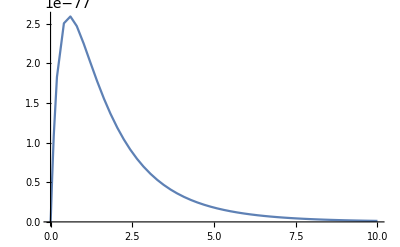

```mathematica
Plot[Evaluate[(J/dg)^2/.Ulow->Ulow Er],{Ulow,0,10}]
```

```mathematica
(J/dg)^2/.Ulow->Ulow Er
```

1.23728×10^-75 ⅇ^(-4. √Ulow) Ulow^(3/2)

```mathematica
Ns = 5;
J[n_,dx]:=
```

## 2D lattice

```mathematica
λtrans = λ813 √2;
f = 7.5 cm;
wh = 300 μm;
wh0=(λ813 f)/(π wh);
zr = (π wh0^2)/λ813;

Pbeamh = 1;
Uh = (16 α Pbeamh)/(ϵ0 c π wh0^2) ;
TrapDepthuK = 10^6 Uh/kB;
TrapDepthHz = 1/(2π)Uh/ℏ;
```

```mathematica
wh0
```

0.0000646965

```mathematica
kh = 2Pi/λtrans;
Erh = (ℏ kh)^2/(2m);
Uh/Erh
```

823.804

```mathematica
Uh=5Erh;
Jh = 4/(√π)Erh(Uh/Erh)^(3/4)Exp[-2 √(Uh/Erh)];
Jhhz = Jh/(2π ℏ)
```

149.581

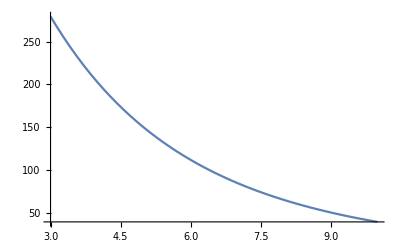

```mathematica
Plot[4/(√π)Erh(U)^(3/4)Exp[-2 √U]/(2π ℏ),{U,3,10}]
```

```mathematica
(λ813 30cm)/(π 292μm)//N
```

0.000265876

```mathematica
π(3.1mm*NA)^2/λ813
```

0.328851

## Number of homogeneous traps

```mathematica
Ulattice = 5Er;
Jtrans = 150*2π ℏ;
xmax = x/.NSolve[Ulattice*(1-Exp[-2x^2/wx0^2])==Jtrans&&x>0,x][[1]];
λtrans = λ813 √2;
2*xmax/λtrans(* Number of sites within J due to axial lattice*)
```

ReplaceAll::reps: {5 (1-ⅇ^Times[«3»]) Er==9.9391×10^-32&&x>0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.73864×10^6 (x/.5 (1-ⅇ^(-(2 x^2)/wx0^2)) Er==9.9391×10^-32&&x>0)

```mathematica
Ulattice/kB
```

9.74693×10^-8

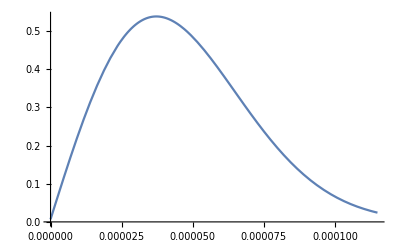

```mathematica
Plot[Ulattice/Jtrans*(Exp[-2x^2/wx0^2]-Exp[-2(x+λtrans)^2/wx0^2]),{x,0,200λtrans}]
```

```mathematica
-Graphics-(*For gaussian beam*)
```